```mathematica
files=FileNames["*.csv",NotebookDirectory[]]
```

{/Users/yaroslav/mipt/bachelor-3/semester-2/laboratory/11.5/data1.csv,/Users/yaroslav/mipt/bachelor-3/semester-2/laboratory/11.5/data.csv}

```mathematica
importfile = files⟦2⟧
```

/Users/yaroslav/mipt/bachelor-3/semester-2/laboratory/11.5/data.csv

```mathematica
"/Users/yaroslav/mipt/bachelor-3/semester-2/laboratory/11.5/data.csv"
```

/Users/yaroslav/mipt/bachelor-3/semester-2/laboratory/11.5/data.csv

```mathematica
raw2= Import[importfile];
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

```mathematica
raw={{"a","n"},{0,653},{10,609},{20,556},{30,525},{40,467},{50,413},{60,367},{70,331},{80,298},{90,268},{103,236}}
```

{{a,n},{0,653},{10,609},{20,556},{30,525},{40,467},{50,413},{60,367},{70,331},{80,298},{90,268},{103,236}}

```mathematica
raw=Union[raw1,raw2]
```

{{0,-0.007},{0.005,0.489},{0.0106,0.95},{0.0149,1.24},{0.02,1.518},{0.025,1.722},{0.0261,1.761},{0.0272,1.794},{0.0281,1.822},{0.0293,1.854},{0.03,1.869},{0.0311,1.894},{0.0319,1.911},{0.033,1.933},{0.0343,1.954},{0.0349,1.963},{0.2534,0.207},{0.2543,0.206},{0.2606,0.201},{0.2616,0.2},{0.2636,0.199},{0.2665,0.198},{0.2941,0.191},{0.3047,0.194},{0.3229,0.21},{0.3467,0.259},{0.3606,0.314},{0.3754,0.41},{0.3871,0.529},{0.391,0.581},{0.3962,0.662},{0.4065,0.877},{0.4137,1.076},{0.4185,1.246},{0.426,1.571},{0.4326,1.942},{0.4388,2.379},{0.4423,2.674},{0.4444,2.861},{0.4504,3.509},{0.4563,4.278},{0.4613,5.059},{U,I}}

```mathematica
raw={{"U","I"},{0,-0.007},{0.005,0.489},{0.0106,0.95},{0.0149,1.24},{0.02,1.518},{0.025,1.722},{0.0261,1.761},{0.0272,1.794},{0.0281,1.822},{0.0293,1.854},{0.03,1.869},{0.0311,1.894},{0.0319,1.911},{0.033,1.933},{0.0343,1.954},{0.0349,1.963},{0.2534,0.207},{0.2543,0.206},{0.2606,0.201},{0.2616,0.2},{0.2636,0.199},{0.2665,0.198},{0.2941,0.191},{0.3047,0.194},{0.3229,0.21},{0.3467,0.259},{0.3606,0.314},{0.3754,0.41},{0.3871,0.529},{0.391,0.581},{0.3962,0.662},{0.4065,0.877},{0.4137,1.076},{0.4185,1.246},{0.426,1.571},{0.4326,1.942},{0.4388,2.379},{0.4423,2.674},{0.4444,2.861},{0.4504,3.509},{0.4563,4.278},{0.4613,5.059}}
```

{{U,I},{0,-0.007},{0.005,0.489},{0.0106,0.95},{0.0149,1.24},{0.02,1.518},{0.025,1.722},{0.0261,1.761},{0.0272,1.794},{0.0281,1.822},{0.0293,1.854},{0.03,1.869},{0.0311,1.894},{0.0319,1.911},{0.033,1.933},{0.0343,1.954},{0.0349,1.963},{0.2534,0.207},{0.2543,0.206},{0.2606,0.201},{0.2616,0.2},{0.2636,0.199},{0.2665,0.198},{0.2941,0.191},{0.3047,0.194},{0.3229,0.21},{0.3467,0.259},{0.3606,0.314},{0.3754,0.41},{0.3871,0.529},{0.391,0.581},{0.3962,0.662},{0.4065,0.877},{0.4137,1.076},{0.4185,1.246},{0.426,1.571},{0.4326,1.942},{0.4388,2.379},{0.4423,2.674},{0.4444,2.861},{0.4504,3.509},{0.4563,4.278},{0.4613,5.059}}

```mathematica
raw1
```

{{U,I},{0.4613,5.059},{0.4563,4.278},{0.4504,3.509},{0.4444,2.861},{0.4423,2.674},{0.4388,2.379},{0.4326,1.942},{0.426,1.571},{0.4185,1.246},{0.4137,1.076},{0.4065,0.877},{0.3962,0.662},{0.391,0.581},{0.3871,0.529},{0.3754,0.41},{0.3606,0.314},{0.3467,0.259},{0.3229,0.21},{0.3047,0.194},{0.2941,0.191},{0.2665,0.198},{0.2636,0.199},{0.2616,0.2},{0.2606,0.201},{0.2543,0.206},{0.2534,0.207}}

```mathematica
dataset=makeDataset[raw]
```

```mathematica
dataset3=dataset1[All,<|"U"->(hiTeXForm[#U]&),"I"->(hiTeXForm[#I]&)|>]
```

Failure[…]

```mathematica
Around[(0.4388+0.4326)/2,(0.4388-0.4326)/2]
```

0.43570.0031

```mathematica
Around[0.15,0.1]-Around[0.0349,0.0006]
```

0.120.10

```mathematica
dataset1=makeDataset[raw]
```

```mathematica
dataset2=makeDataset[raw]
```

```mathematica
dataset1=dataset[All,<|"a"->(1/Around[#n,1]&),"b"->(1-Cos[ π Around[#a,1] /180]&)|>]
```

```mathematica
MantErr[a_]:=If[10≤Round[FromDigits[RealDigits[a["Uncertainty"]]⟦1,;;3⟧],10]/10≤19,Round[FromDigits[RealDigits[a["Uncertainty"]]⟦1,;;3⟧],10]/10,Round[FromDigits[RealDigits[a["Uncertainty"]]⟦1,;;2⟧],10]/10]
MantExp[a_]:=If[10≤Round[FromDigits[RealDigits[a["Uncertainty"]]⟦1,;;3⟧],10]/10≤19,MantissaExponent[a["Uncertainty"]]⟦2⟧-2,MantissaExponent[a["Uncertainty"]]⟦2⟧-1]
DigVal[a_]:=MantissaExponent[a["Value"]]⟦2⟧-MantExp[a]+1
MantVal[a_]:=Round[FromDigits[RealDigits[a["Value"]]⟦1,;;DigVal[a]⟧],10]/10
hiTeXForm[x_]:=Which[Head[x]===Real,IntegerPart[x],-3≤MantExp[x]≤-1,ToString[Row[{PaddedForm[MantVal[x]*10.^MantExp[x],{DigVal[x],Abs[MantExp[x]]},NumberPadding->{"","0"}],"(",MantErr[x],")"}]],MantExp[x]==0,ToString[Row[{MantVal[x],"(",MantErr[x],")"}]],True,ToString[Row[{MantVal[x],"(",MantErr[x],")e",MantExp[x]}]]]
hiTeXFormVal[x_]:=Which[Head[x]===Real,IntegerPart[x],MantExp[x]≠0,ToString[PaddedForm[x["Value"],{DigVal[x],Abs[MantExp[x]]},NumberPadding->{"","0"}]],MantExp[x]==0,MantVal[x]]
hiTeXFormErr[x_]:=Which[Head[x]===Real,IntegerPart[x],MantExp[x]≠0,ToString[PaddedForm[MantErr[x]*10.^MantExp[x],{DigVal[x],Abs[MantExp[x]]},NumberPadding->{"","0"}]],MantExp[x]==0,MantErr[x]]
```

```mathematica
dataset3=dataset1[All,<|"aexp"->(hiTeXForm[#a]&),"bexp"->(hiTeXForm[#b]&)|>]
```

```mathematica
dataset4=dataset1[All,<|"TexpAbs"->(hiTeXFormVal[#T]&),"TexpErr"->(hiTeXFormErr[#T]&),"WexpAbs"->(hiTeXFormVal[#W]&),"WexpErr"->(hiTeXFormErr[#W]&)|>]
```

```mathematica
Export[NotebookDirectory[]<>"datasethi.csv",dataset,"TextDelimiters"->""]
```

/Users/yaroslav/mipt/bachelor-3/semester-2/laboratory/11.5/datasethi.csv

```mathematica
raw={Table[n+RandomInteger[],{n,10}],Table[n,{n,10}]}
```

{{2,2,3,4,6,7,7,8,9,11},{1,2,3,4,5,6,7,8,9,10}}

```mathematica
data=Table[{dataset2[n,"LnT"]["Value"],dataset2[n,"LnW"]["Value"]},{n,11}];
dataerr=Table[{dataset2[n,"LnT"],dataset2[n,"LnW"]},{n,11}];
fit=LinearModelFit[data,{1,x},x](*   f = a + b * x   *)
fit["ParameterTable"];
a=Around[fit["BestFitParameters"]⟦1⟧,fit["ParameterErrors"]⟦1⟧]
b=Around[fit["BestFitParameters"]⟦2⟧,fit["ParameterErrors"]⟦2⟧]
(*fit["BestFitParameters"]⟦1⟧
fit["BestFitParameters"]⟦2⟧*)
(*hiTeXForm[a]
hiTeXForm[b]*)
Show[ListPlot[dataerr],Plot[fit["BestFitParameters"]⟦1⟧+fit["BestFitParameters"]⟦2⟧x,{x,Min[data⟦All,1⟧],Max[data⟦All,1⟧]}]]
```

FittedModel[-0.233216+0.971731 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.233216 | 0.385588 | -0.60483 | 0.56205
x | 0.971731 | 0.0585976 | 16.5831 | 1.76621×10^-7

-0.20.4

0.970.06

0.2(4)

0.97(6)

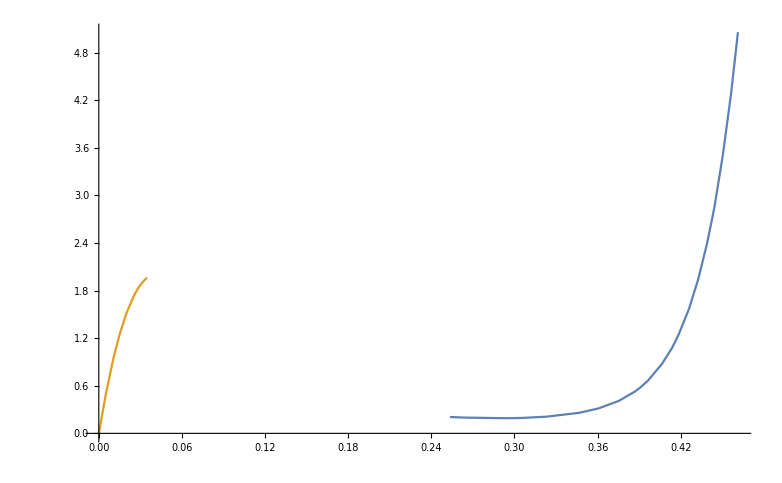

```mathematica
ListLinePlot[{dataset,dataset2}]
```

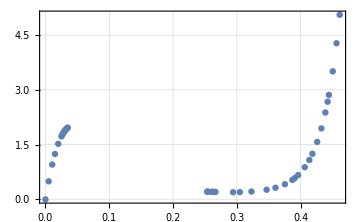

```mathematica
ListPlot[dataset,Frame->True,FrameStyle->Black,GridLines->Automatic,ImageSize->Medium,LabelStyle->{NumberPoint->","},BaseStyle->{FontFamily->"CMU Serif"},(*PlotLegends->MaTeX@functions,*)FrameLabel->MaTeX@{"U,\\text{ В}","I,\\text{ мА}"}]
```

```mathematica
files=FileNames["*.heic",NotebookDirectory[]]
```

{/Users/yaroslav/mipt/bachelor-3/semester-2/laboratory/11.5/IMG_3208.HEIC,/Users/yaroslav/mipt/bachelor-3/semester-2/laboratory/11.5/IMG_3209.HEIC,/Users/yaroslav/mipt/bachelor-3/semester-2/laboratory/11.5/IMG_3210.HEIC,/Users/yaroslav/mipt/bachelor-3/semester-2/laboratory/11.5/IMG_3211.HEIC,/Users/yaroslav/mipt/bachelor-3/semester-2/laboratory/11.5/IMG_3212.HEIC,/Users/yaroslav/mipt/bachelor-3/semester-2/laboratory/11.5/IMG_3213.HEIC,/Users/yaroslav/mipt/bachelor-3/semester-2/laboratory/11.5/IMG_3214.HEIC,/Users/yaroslav/mipt/bachelor-3/semester-2/laboratory/11.5/IMG_3215.HEIC,/Users/yaroslav/mipt/bachelor-3/semester-2/laboratory/11.5/IMG_3216.HEIC}